### Basic Examples (3)

Construct a simple Petri net from lists of four places, three transitions and eight arcs, with an initial distribution of six tokens:

```mathematica
petriNet=ResourceFunction["MakePetriNet"][{p1,p2,p3,p4},{t1,t2,t3},{p1->t1,t1->p1,p2->t1,p3->t1,t2->p2,p3->t3,t3->p4,p4->t2},{1,2,1,2}]
```

PetriNetObject[…]

Evaluate one step in the multiway evolution of this Petri net:

```mathematica
[petriNet]
```

{PetriNetObject[…],PetriNetObject[…],PetriNetObject[…]}

Evaluate the first three steps in the multiway evolution of this Petri net:

```mathematica
[petriNet,3]
```

{{PetriNetObject[…]},{PetriNetObject[…],PetriNetObject[…],PetriNetObject[…]},{PetriNetObject[…],PetriNetObject[…],PetriNetObject[…]},{PetriNetObject[…],PetriNetObject[…]}}

Show the set of labeled graphs obtained after one step, with every possible transition firing highlighted:

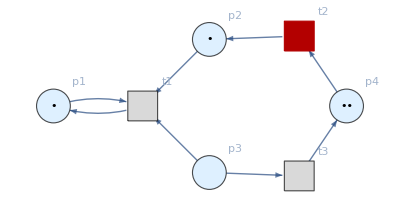
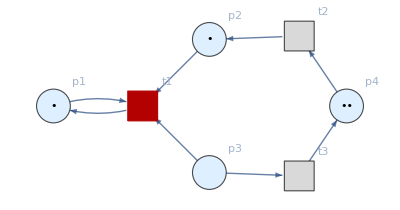
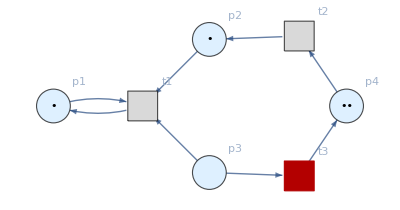
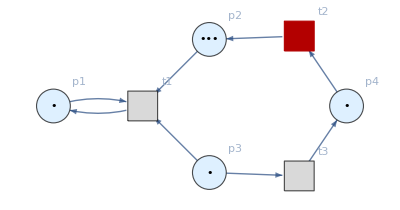
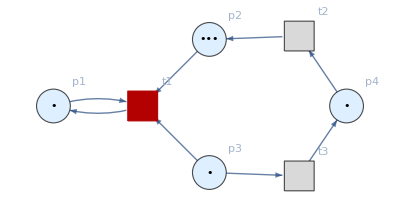
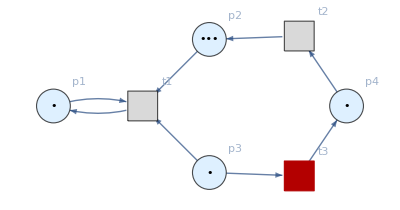
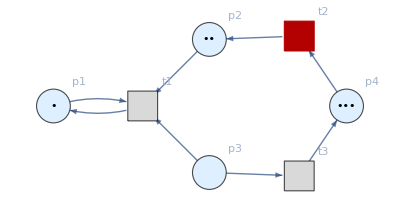
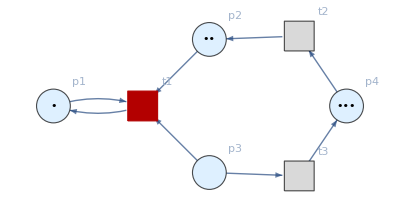

```mathematica
[petriNet,"LabeledGraphsHighlighted"]
```

Show the set of labeled graphs obtained after one step, but without any transition firings highlighted:

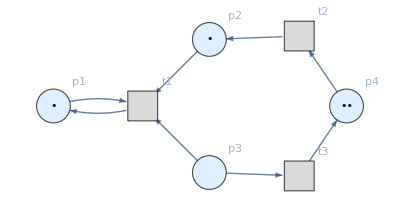
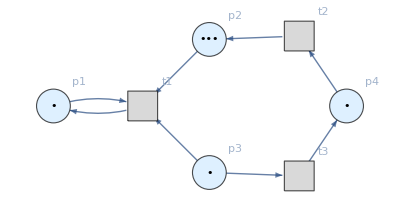
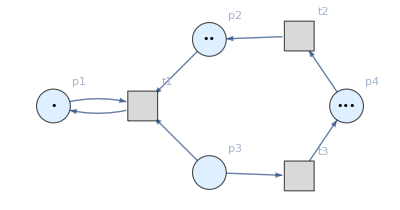

```mathematica
[petriNet,"LabeledGraphs"]
```

Show the sets of labeled graphs after three steps, without any transition firings highlighted:

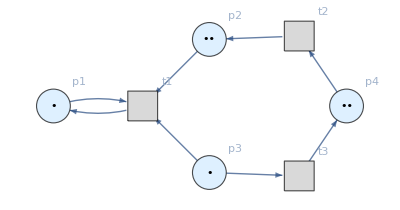
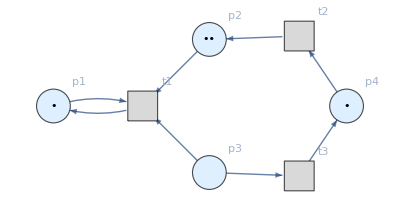
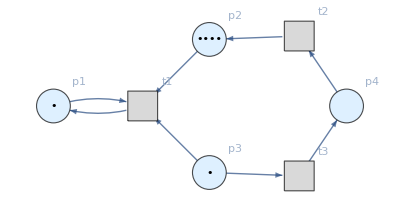
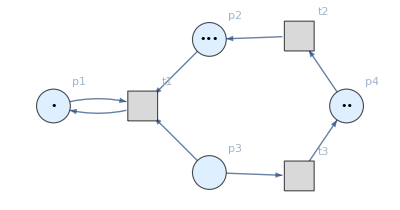
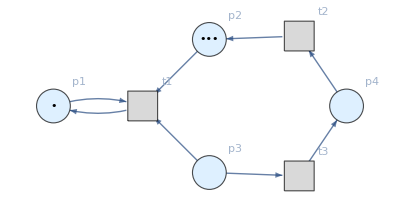
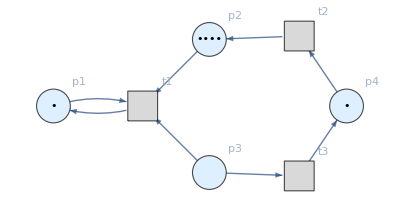
{{-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
[petriNet,3,"LabeledGraphs"]
```

Evolve a Petri net (representing a reversible chemical reaction) specified by an association of three places, two transitions and six arcs, with an initial distribution of twelve tokens, for three steps:

```mathematica
[<|"Places"->{"O2","H2O","H2"},"Transitions"->{"Hydrolysis","Combination"},"Arcs"->{"Hydrolysis"->"O2","O2"->"Combination","Combination"->"H2O","H2O"->"Hydrolysis","Hydrolysis"->"H2","H2"->"Combination"}|>,{1,4,7},3]
```

{{PetriNetObject[…]},{PetriNetObject[…],PetriNetObject[…]},{PetriNetObject[…],PetriNetObject[…]},{PetriNetObject[…],PetriNetObject[…],PetriNetObject[…]}}

Show the lists of token numbers obtained after each of the three steps:

```mathematica
[<|"Places"->{"O2","H2O","H2"},"Transitions"->{"Hydrolysis","Combination"},"Arcs"->{"Hydrolysis"->"O2","O2"->"Combination","Combination"->"H2O","H2O"->"Hydrolysis","Hydrolysis"->"H2","H2"->"Combination"}|>,{1,4,7},3,"Tokens"]
```

{{{1,4,7}},{{2,3,8},{0,5,6}},{{3,2,9},{1,4,7}},{{4,1,10},{2,3,8},{0,5,6}}}

Show the lists of token numbers obtained after each of the three steps, along with the corresponding transition firings:

```mathematica
[<|"Places"->{"O2","H2O","H2"},"Transitions"->{"Hydrolysis","Combination"},"Arcs"->{"Hydrolysis"->"O2","O2"->"Combination","Combination"->"H2O","H2O"->"Hydrolysis","Hydrolysis"->"H2","H2"->"Combiantion"}|>,{1,4,7},3,"TokenFirings"]
```

{{{{1,4,7},Null}},{{{2,3,8},Hydrolysis},{{2,3,8},Combination},{{0,5,7},Hydrolysis},{{0,5,7},Combination}},{{{3,2,9},Hydrolysis},{{3,2,9},Combination},{{1,4,8},Hydrolysis},{{1,4,8},Combination}},{{{4,1,10},Hydrolysis},{{4,1,10},Combination},{{2,3,9},Hydrolysis},{{2,3,9},Combination},{{0,5,8},Hydrolysis},{{0,5,8},Combination}}}

Show the sets of labeled graphs obtained after two steps, with every possible transition firing highlighted:

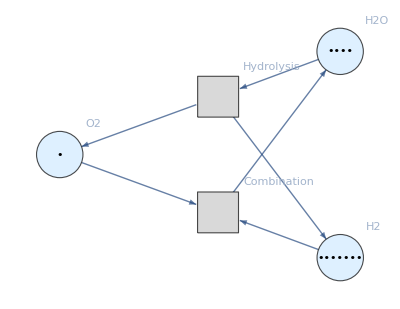
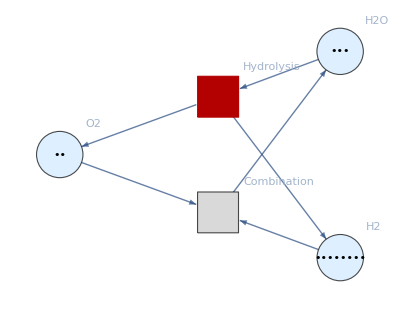
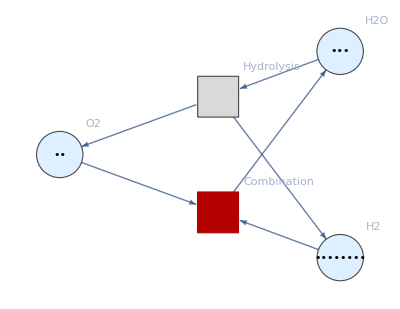
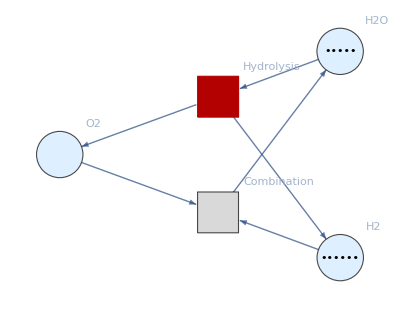
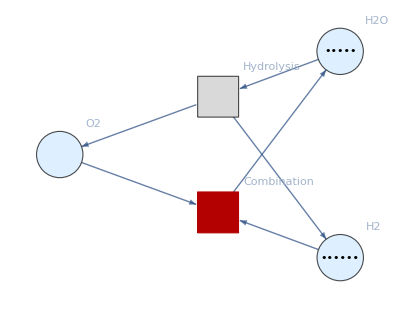
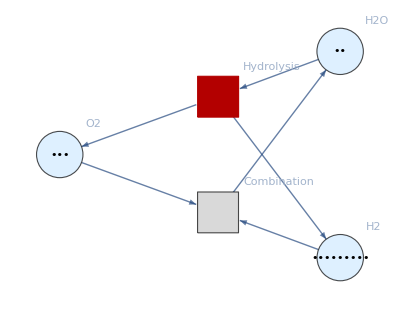
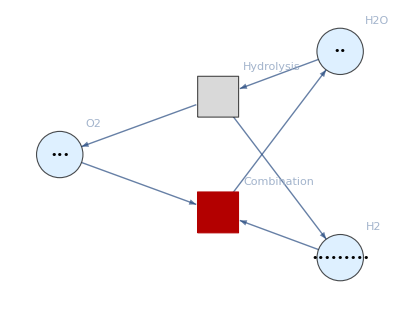
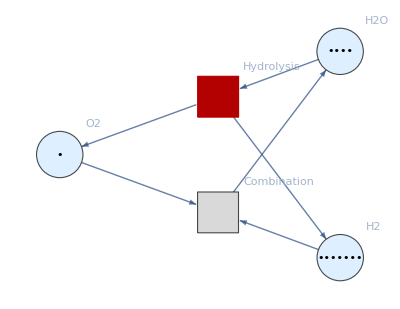

```mathematica
[<|"Places"->{"O2","H2O","H2"},"Transitions"->{"Hydrolysis","Combination"},"Arcs"->{"Hydrolysis"->"O2","O2"->"Combination","Combination"->"H2O","H2O"->"Hydrolysis","Hydrolysis"->"H2","H2"->"Combination"}|>,{1,4,7},2,"LabeledGraphsHighlighted"]
```

Show the sets of weighted graphs obtained after two steps, with every possible transition firing highlighted:

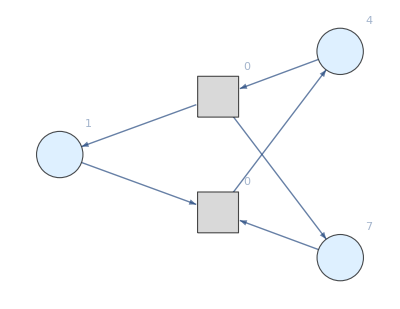
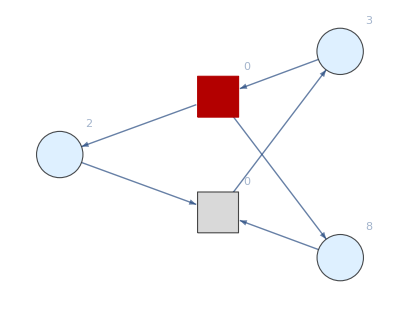
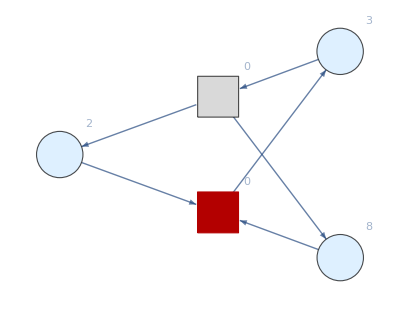
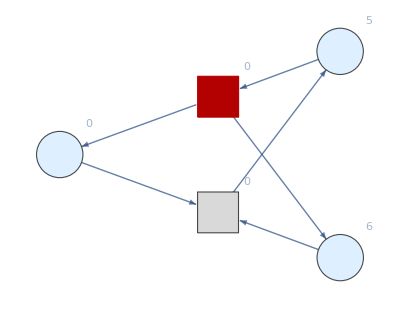
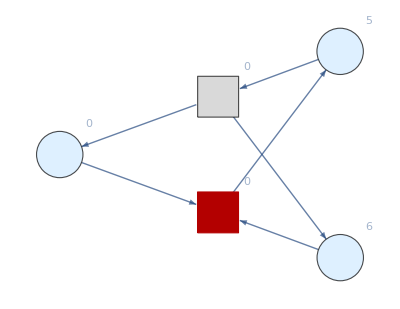
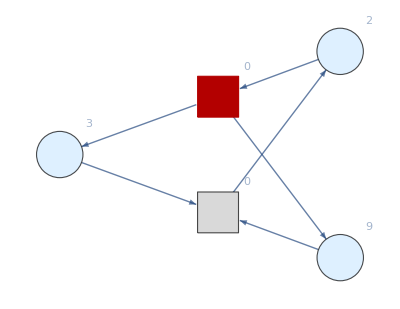
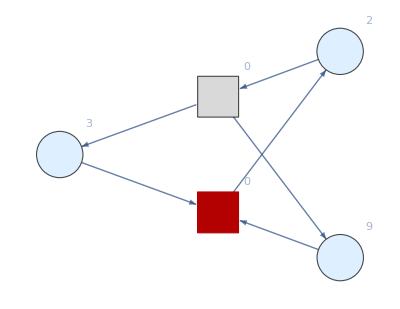
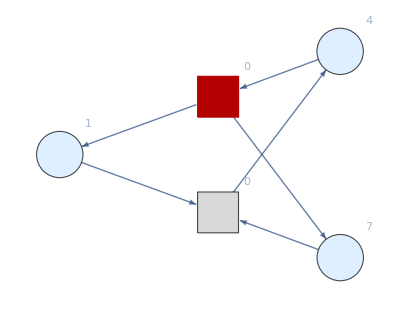

```mathematica
[<|"Places"->{"O2","H2O","H2"},"Transitions"->{"Hydrolysis","Combination"},"Arcs"->{"Hydrolysis"->"O2","O2"->"Combination","Combination"->"H2O","H2O"->"Hydrolysis","Hydrolysis"->"H2","H2"->"Combination"}|>,{1,4,7},2,"WeightedGraphsHighlighted",VertexLabels->"VertexWeight"]
```

Show the sets of weighted graphs obtained after two steps, but without any transition firings highlighted:

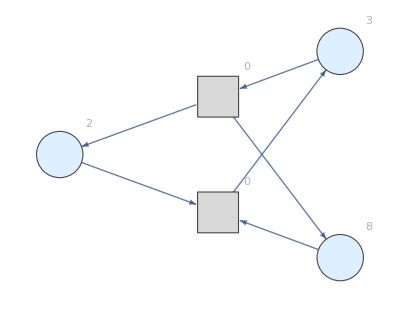
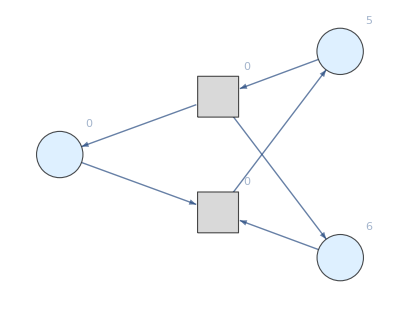
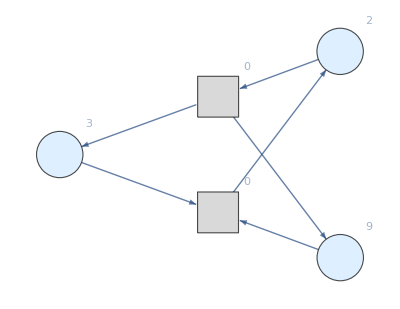
{{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
[<|"Places"->{"O2","H2O","H2"},"Transitions"->{"Hydrolysis","Combination"},"Arcs"->{"Hydrolysis"->"O2","O2"->"Combination","Combination"->"H2O","H2O"->"Hydrolysis","Hydrolysis"->"H2","H2"->"Combination"}|>,{1,4,7},2,"WeightedGraphs",VertexLabels->"VertexWeight"]
```

Evolve a more complicated Petri net representing a concurrent communications protocol between two agents (specified as lists of places, transitions, arcs and tokens) for two steps:

```mathematica
[{p1,p2,p3,p4,p5,p6,p7,p8},{"Person 1","Person 2","Send Message","Receive Message","Receive Acknowledgement","Send Acknowledgement"},{"Person 1"->p1,p1->"Send Message","Send Message"->p3,"Send Message"->p4,p3->"Receive Message",p4->"Receive Acknowledgement","Receive Acknowledgement"->p7,p7->"Person 1","Receive Message"->p5,p5->"Send Acknowledgement","Send Acknowledgement"->p6,"Send Acknowledgement"->p8,p8->"Person 2","Person 2"->p2,p2->"Receive Message",p6->"Receive Acknowledgement"},{0,2,0,6,1,1,2,1},2]
```

{{PetriNetObject[…]},{PetriNetObject[…],PetriNetObject[…],PetriNetObject[…],PetriNetObject[…]},{PetriNetObject[…],PetriNetObject[…],PetriNetObject[…],PetriNetObject[…],PetriNetObject[…],PetriNetObject[…],PetriNetObject[…],PetriNetObject[…]}}

Show the lists of token numbers obtained after each of the two steps, along with the corresponding transition firings:

```mathematica
[{p1,p2,p3,p4,p5,p6,p7,p8},{"Person 1","Person 2","Send Message","Receive Message","Receive Acknowledgement","Send Acknowledgement"},{"Person 1"->p1,p1->"Send Message","Send Message"->p3,"Send Message"->p4,p3->"Receive Message",p4->"Receive Acknowledgement","Receive Acknowledgement"->p7,p7->"Person 1","Receive Message"->p5,p5->"Send Acknowledgement","Send Acknowledgement"->p6,"Send Acknowledgement"->p8,p8->"Person 2","Person 2"->p2,p2->"Receive Message",p6->"Receive Acknowledgement"},{0,2,0,6,1,1,2,1},2,"TokenFirings"]
```

{{{{0,2,0,6,1,1,2,1},Null}},{{{1,2,0,6,1,1,1,1},Person 1},{{1,2,0,6,1,1,1,1},Person 2},{{1,2,0,6,1,1,1,1},Send Message},{{1,2,0,6,1,1,1,1},Receive Acknowledgement},{{1,2,0,6,1,1,1,1},Send Acknowledgement},{{0,3,0,6,1,1,2,0},Person 1},{{0,3,0,6,1,1,2,0},Person 2},{{0,3,0,6,1,1,2,0},Send Message},{{0,3,0,6,1,1,2,0},Receive Acknowledgement},{{0,3,0,6,1,1,2,0},Send Acknowledgement},{{0,2,0,5,1,0,3,1},Person 1},{{0,2,0,5,1,0,3,1},Person 2},{{0,2,0,5,1,0,3,1},Send Message},{{0,2,0,5,1,0,3,1},Receive Acknowledgement},{{0,2,0,5,1,0,3,1},Send Acknowledgement},{{0,2,0,6,0,2,2,2},Person 1},{{0,2,0,6,0,2,2,2},Person 2},{{0,2,0,6,0,2,2,2},Send Message},{{0,2,0,6,0,2,2,2},Receive Acknowledgement},{{0,2,0,6,0,2,2,2},Send Acknowledgement}},{{{2,2,0,6,1,1,0,1},Person 2},{{2,2,0,6,1,1,0,1},Send Message},{{2,2,0,6,1,1,0,1},Receive Acknowledgement},{{2,2,0,6,1,1,0,1},Send Acknowledgement},{{2,2,0,6,1,1,0,1},Person 1},{{2,2,0,6,1,1,0,1},Receive Message},{{1,3,0,6,1,1,1,0},Person 2},{{1,3,0,6,1,1,1,0},Send Message},{{1,3,0,6,1,1,1,0},Receive Acknowledgement},{{1,3,0,6,1,1,1,0},Send Acknowledgement},{{1,3,0,6,1,1,1,0},Person 1},{{1,3,0,6,1,1,1,0},Receive Message},{{0,2,1,7,1,1,1,1},Person 2},{{0,2,1,7,1,1,1,1},Send Message},{{0,2,1,7,1,1,1,1},Receive Acknowledgement},{{0,2,1,7,1,1,1,1},Send Acknowledgement},{{0,2,1,7,1,1,1,1},Person 1},{{0,2,1,7,1,1,1,1},Receive Message},{{1,2,0,5,1,0,2,1},Person 2},{{1,2,0,5,1,0,2,1},Send Message},{{1,2,0,5,1,0,2,1},Receive Acknowledgement},{{1,2,0,5,1,0,2,1},Send Acknowledgement},{{1,2,0,5,1,0,2,1},Person 1},{{1,2,0,5,1,0,2,1},Receive Message},{{1,2,0,6,0,2,1,2},Person 2},{{1,2,0,6,0,2,1,2},Send Message},{{1,2,0,6,0,2,1,2},Receive Acknowledgement},{{1,2,0,6,0,2,1,2},Send Acknowledgement},{{1,2,0,6,0,2,1,2},Person 1},{{1,2,0,6,0,2,1,2},Receive Message},{{0,3,0,5,1,0,3,0},Person 1},{{0,3,0,5,1,0,3,0},Send Message},{{0,3,0,5,1,0,3,0},Receive Acknowledgement},{{0,3,0,5,1,0,3,0},Send Acknowledgement},{{0,3,0,5,1,0,3,0},Person 2},{{0,3,0,6,0,2,2,1},Person 1},{{0,3,0,6,0,2,2,1},Send Message},{{0,3,0,6,0,2,2,1},Receive Acknowledgement},{{0,3,0,6,0,2,2,1},Send Acknowledgement},{{0,3,0,6,0,2,2,1},Person 2},{{0,2,0,5,0,1,3,2},Person 1},{{0,2,0,5,0,1,3,2},Person 2},{{0,2,0,5,0,1,3,2},Send Message},{{0,2,0,5,0,1,3,2},Send Acknowledgement},{{0,2,0,5,0,1,3,2},Receive Acknowledgement}}}

### Scope (2)

If PetriNetMultiwayEvolution is called without an explicit list of token numbers, it is assumed that each place contains no tokens:

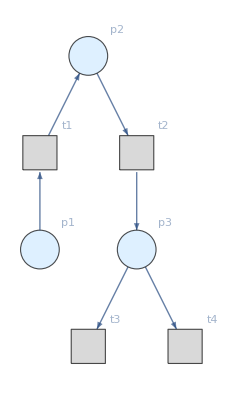

```mathematica
[{p1,p2,p3},{t1,t2,t3,t4},{p1->t1,t1->p2,p2->t2,t2->p3,p3->t3,p3->t4},1,"LabeledGraphs"]
```

Construct a Petri net representing a simple producer-consumer problem in concurrency theory:

```mathematica
petriNet=ResourceFunction["MakePetriNet"][{p1,p2,p3,"Buffer",p4},{"Produce",t1,t2,"Consume"},{p1->"Produce","Produce"->p3,p3->t2,t2->p1,t2->"Buffer","Buffer"->t1,t1->p4,p4->"Consume","Consume"->p2,p2->t1},{1,3,0,6,2}]
```

PetriNetObject[…]

Show the list of Petri net objects obtained after two steps of multiway evolution:

```mathematica
[petriNet,2,"PetriNetObjects"]
```

{{PetriNetObject[…]},{PetriNetObject[…],PetriNetObject[…],PetriNetObject[…]},{PetriNetObject[…],PetriNetObject[…],PetriNetObject[…],PetriNetObject[…],PetriNetObject[…],PetriNetObject[…]}}

Show the list of directed graph representations (with token counts represented graphically) after two steps of multiway evolution:

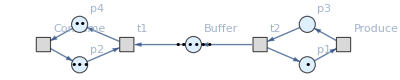
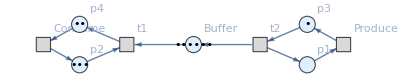
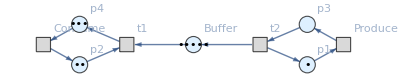
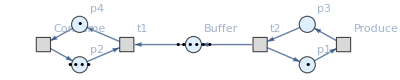
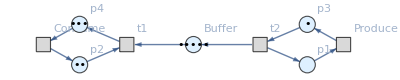
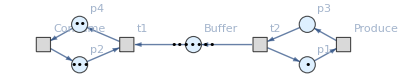
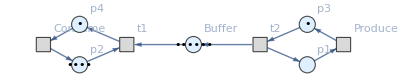
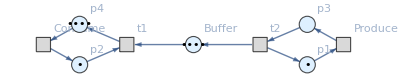

```mathematica
[petriNet,2,"LabeledGraphs"]
```

Show the list of directed graph representations (with token counts represented graphically, and with transition firings highlighted) after two steps of multiway evolution:

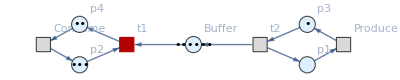
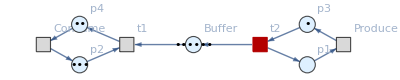
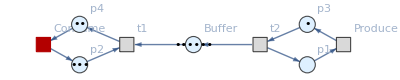
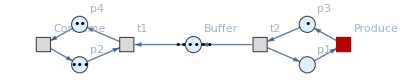
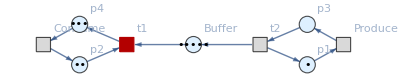
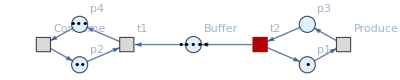
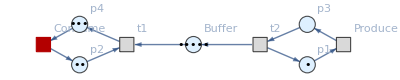
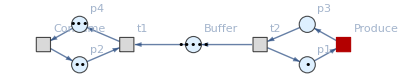
{{-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
[petriNet,2,"LabeledGraphsHighlighted"]
```

Show the list of directed graph representations (with token counts represented as vertex weights) after two steps of multiway evolution:

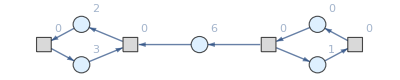
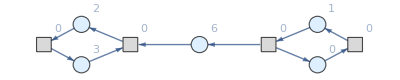
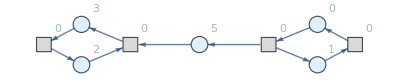
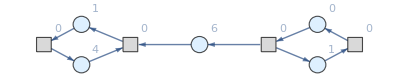
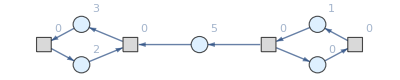
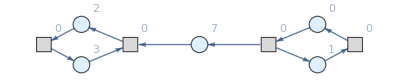
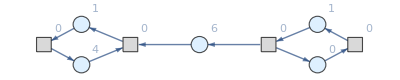
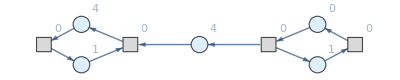

```mathematica
[petriNet,2,"WeightedGraphs",VertexLabels->"VertexWeight"]
```

Show the list of directed graph representations (with token counts represented as vertex weights, and with transition firings highlighted) after two steps of multiway evolution:

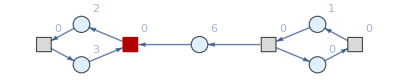
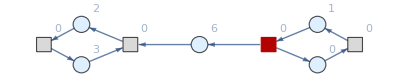
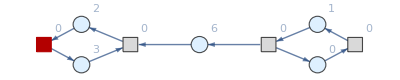
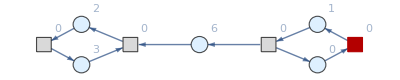
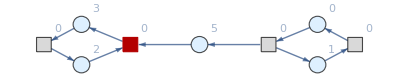
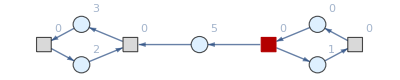
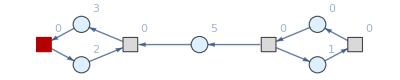
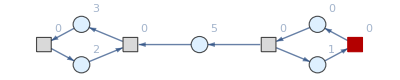
{{-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
[petriNet,2,"WeightedGraphsHighlighted",VertexLabels->"VertexWeight"]
```

Show the list of token numbers associated to each place after each firing, following two steps of multiway evolution:

```mathematica
[petriNet,2,"Tokens"]
```

{{{1,3,0,6,2}},{{0,3,1,6,2},{1,2,0,5,3},{1,4,0,6,1}},{{0,2,1,5,3},{1,3,0,7,2},{0,4,1,6,1},{1,1,0,4,4},{1,3,0,5,2},{1,5,0,6,0}}}

Show the list of token numbers associated to each place after each firing (with the corresponding transition firings specified), following two steps of multiway evolution:

```mathematica
[petriNet,2,"TokenFirings"]
```

{{{{1,3,0,6,2},Null}},{{{0,3,1,6,2},t1},{{0,3,1,6,2},t2},{{0,3,1,6,2},Consume},{{0,3,1,6,2},Produce},{{1,2,0,5,3},t1},{{1,2,0,5,3},t2},{{1,2,0,5,3},Consume},{{1,2,0,5,3},Produce},{{1,4,0,6,1},t1},{{1,4,0,6,1},t2},{{1,4,0,6,1},Consume},{{1,4,0,6,1},Produce}},{{{0,2,1,5,3},t1},{{0,2,1,5,3},t2},{{0,2,1,5,3},Consume},{{0,2,1,5,3},Produce},{{1,3,0,7,2},t1},{{1,3,0,7,2},t2},{{1,3,0,7,2},Consume},{{1,3,0,7,2},Produce},{{0,4,1,6,1},t1},{{0,4,1,6,1},t2},{{0,4,1,6,1},Consume},{{0,4,1,6,1},Produce},{{1,1,0,4,4},t1},{{1,1,0,4,4},t2},{{1,1,0,4,4},Consume},{{1,1,0,4,4},Produce},{{1,3,0,5,2},t1},{{1,3,0,5,2},t2},{{1,3,0,5,2},Consume},{{1,3,0,5,2},Produce},{{1,5,0,6,0},t1},{{1,5,0,6,0},t2},{{1,5,0,6,0},Consume},{{1,5,0,6,0},Produce}}}

### Options (1)

PetriNetMultiwayEvolution supports the same options as Graph:

```mathematica
[{p1,p2,p3,p4},{t1,t2,t3},{p1->t1,t1->p1,p2->t1,p3->t1,t2->p2,p3->t3,t3->p4,p4->t2},{1,2,1,2},"LabeledGraphs"]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
[{p1,p2,p3,p4},{t1,t2,t3},{p1->t1,t1->p1,p2->t1,p3->t1,t2->p2,p3->t3,t3->p4,p4->t2},{1,2,1,2},"LabeledGraphs",VertexSize->0.1]
```

{-Graphics-,-Graphics-,-Graphics-}